```mathematica
(*soo i wanna make a code that does the cross section as a function of the input frequency - bc it is the most interesting so far lets just focus on the simplest possible stimulated emission process so far*)
(*Here I load everything I need*)
g=1.5;
κ=1;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p5"];
PhiVSYKappa1G1p5=Interpolation[PhiVsYListKappa1G1p5,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p5[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-150,150,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[Pi]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;

L=300;
total=800;
dx=.01;
vals=Import["/scratch/network/zz3250/valsL300dxp01g1p5_total800.wl"];
fns=Import["/scratch/network/zz3250/vecsL300dxp01g1p5_total800.wl"];
```

```mathematica
(*Making consistent the sign of the eigenvectors*)
a=fns[[1]]/.x->0;
If[a<0,fns[[1]]=-fns[[1]]];
For[i=2,i<=total,i=i+2,
a=fns[[i]]/.x->-.1;
If[a<0,fns[[i]]=-fns[[i]]];
];
For[i=3,i<=total,i=i+2,
a=fns[[i]]/.x->0;
If[a>0,fns[[i]]=-fns[[i]]];
];
```

```mathematica
2*Sqrt[vals[[1]]]
Sqrt[vals[[199]]]
3*Sqrt[vals[[1]]]
Sqrt[vals[[432]]]
```

3.58797

3.58529

5.38196

5.38282

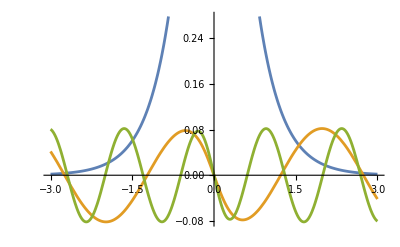

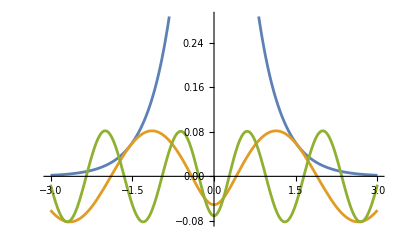

```mathematica
Plot[{fns[[1]],fns[[198]],fns[[432]]},{x,-3,3}]
Plot[{fns[[1]],fns[[199]],fns[[431]]},{x,-3,3}]
```

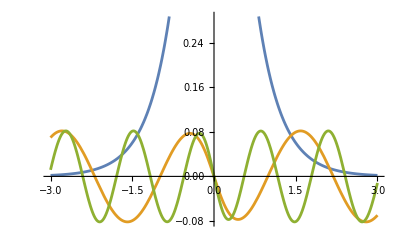

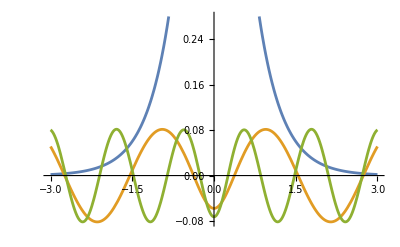

```mathematica
Plot[{fns[[1]],fns[[250]],fns[[484]]},{x,-3,3}]
Plot[{fns[[1]],fns[[251]],fns[[483]]},{x,-3,3}]
```

```mathematica
(*ABSORPTION*)
kstart=355;
deltaWidth=.1;
mSqList={};
klist={};
For[k=kstart,k<=total,k=k+2,
energyIn=Sqrt[vals[[k]]];
mSq=0;
p1={};
For[i=3,i<=total,i=i+2,
If [Abs[Sqrt[vals[[i]]]+Sqrt[vals[[1]]]-energyIn]<=deltaWidth,
AppendTo[p1,i]];
];
For[i=1,i<=Length[p1],i++,
coeff=Pi^2*κ^2/(Sqrt[vals[[1]]]*Sqrt[vals[[k]]])*(1/Sqrt[vals[[p1[[i]]]]-g^2-2*Pi*κ]);
dk[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2]; (*Always moving right*)
(*R->L*)
dp1[x_]:=(fns[[p1[[i]]]]-I*fns[[p1[[i]]-1]])/Sqrt[2];
mleft=NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dk[x]*dp1[x],{x,-L/2,L/2}];
(*R->R*)
dp1[x_]:=(fns[[p1[[i]]]]+I*fns[[p1[[i]]-1]])/Sqrt[2];
mright=NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dk[x]*dp1[x],{x,-L/2,L/2}];
amplitude=coeff*(Abs[mleft]^2+Abs[mright]^2);
mSq=mSq+amplitude;
];
mSq=mSq/Length[p1];
AppendTo[mSqList,mSq];
AppendTo[klist,k];
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 3.12348×10^-8+0.0000239937 ⅈ and 9.78102×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -9.78613×10^-9-7.24566×10^-6 ⅈ and 2.38176×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 6.24042×10^-8+0.0000479432 ⅈ and 1.9524×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

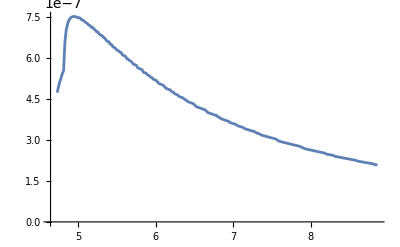

```mathematica
ListLinePlot[Transpose[{Sqrt[vals[[klist]]],mSqList}]]
```

```mathematica
(*Calculating invariant matrix element for each possible input energy*)
kstart=3;
deltaWidth=.1;
mSqList={};
klist={};
For[k=kstart,k<=total,k=k+2,
energyIn=Sqrt[vals[[k]]]+Sqrt[vals[[1]]];
mSq=0;
(*Check which possible outputs are within the acceptable delta width*)
p1={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-energyIn]<=deltaWidth,
AppendTo[p1,i]];
];
(*Loop over all possible outputs and add up the amplitudes*)
For[i=1,i<=Length[p1],i++,
dk[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
(*R->L*)
dp1[x_]:=(fns[[p1[[i]]]]-I*fns[[p1[[i]]-1]])/Sqrt[2];
mref=NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*dk[x]*dp1[x]*fns[[1]],{x,-L/2,L/2}];
(*R->R*)
dp1[x_]:=(fns[[p1[[i]]]]+I*fns[[p1[[i]]-1]])/Sqrt[2];
mtrans=NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*dk[x]*dp1[x]*fns[[1]],{x,-L/2,L/2}];
coeff=Pi^2*κ^2/(Sqrt[vals[[1]]]*Sqrt[vals[[k]]])*(1/Sqrt[vals[[p1[[i]]]]-g^2-2*Pi*κ]);
mSq=mSq+coeff*(Abs[mref]^2+Abs[mtrans]^2);
];
mSq=mSq/Length[p1];
AppendTo[mSqList,mSq];
AppendTo[klist,k];
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 2.92355×10^-8-0.0000230364 ⅈ and 9.37318×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -8.81812×10^-9-6.71196×10^-6 ⅈ and 2.28407×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 2.95666×10^-8-0.0000232003 ⅈ and 9.44004×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

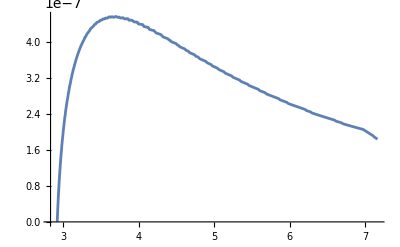

```mathematica
ListLinePlot[Transpose[{Sqrt[vals[[klist]]],mSqList}]]
```